## Newton Decrement

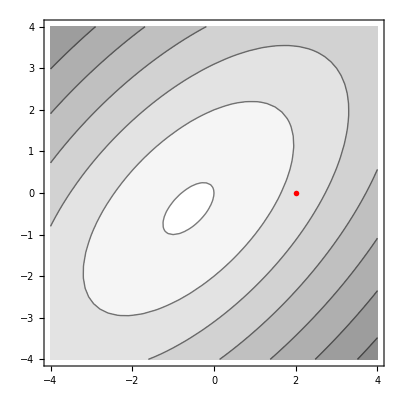

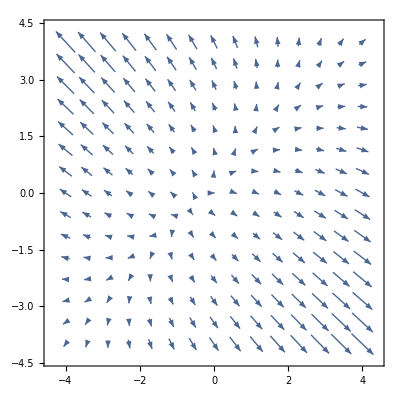

```mathematica
g=RotationMatrix[Pi/4];
A=g.{{1,0},{0,4}}.Inverse[g];
b=v2c@{1,0};
c=4;
loss[x_]:=toscalar[1/2 xᵀ.A.x+bᵀ.x+4];
grad[x_]:=A.x+b;
xvar={x1,x2};
plt1=ContourPlot[Sqrt@loss[v2c@{x1,x2}],{x1,-4,4},{x2,-4,4},ColorFunction->Function[GrayLevel[1 - .45 #]]];
Show[plt1,Graphics[{Red,PointSize[0.01],Point[c2v@w0]}]]
w0=v2c@{2,0};
grads=D[loss[v2c@{x1,x2}],{{x1,x2},1}];
VectorPlot@@{grads,{x1,-4,4},{x2,-4,4}}
```

### Minimize

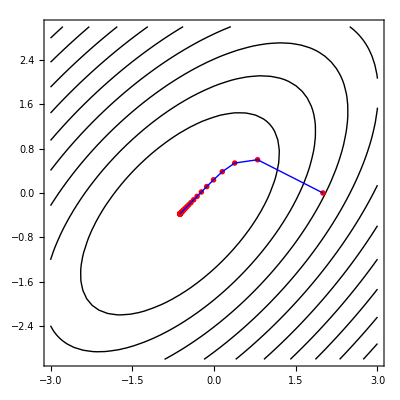

```mathematica
bound=3;
pointList={};
gradList={};
lossList={};
iters=10;
w=w0;
lr=0.2;
iters=50;
For[iter=1,iter≤iters,iter++,pointList=pointList~Append~w;
gradList=gradList~Append~grad[w];
lossList=lossList~Append~loss[w];
w=w-lr*grad[w]
];

plt1=ContourPlot[Sqrt@loss[v2c@{x,y}],{x,-bound,bound},{y,-bound,bound},Contours->10,ContourShading->None];
plotPoints=Flatten/@pointList[[;;50]];
plt2=Graphics[{Red,PointSize[0.01],Point[plotPoints]}];
plt3=Graphics[{Blue,Line[plotPoints]}];
Show[plt1,plt2,plt3]
```

#### Plot in whitened coordinates

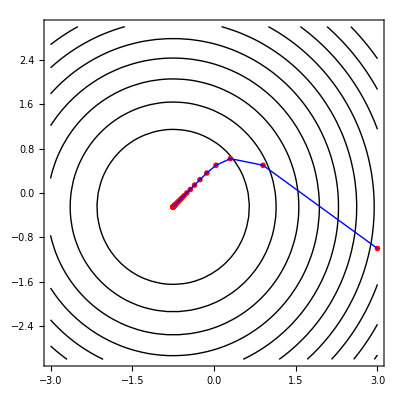

```mathematica
whiten=Inverse@symsqrt[A];
unwhiten=symsqrt[A];
plt1=ContourPlot[Sqrt@loss[whiten.v2c@{x,y}],{x,-bound,bound},{y,-bound,bound},Contours->10,ContourShading->None];
plotPoints2=unwhiten.#&/@(Flatten/@pointList[[;;50]]);
plt2=Graphics[{Red,PointSize[0.01],Point[plotPoints2]}];
plt3=Graphics[{Blue,Line[plotPoints2]}];
Show[plt1,plt2,plt3]
```

#### Take Newton step

```mathematica
loss[w0]
```

11

```mathematica
wopt=-Inverse[A].b;
loss[wopt]//N
```

3.6875

```mathematica
lambda=symsqrt[grad[w0]ᵀ.Inverse[A].grad[w0]]//Simplify
```

{{(3 √(13/2))/2}}

```mathematica
toscalar[lambda^2/2+loss[wopt]]==loss[w0]
```

True

```mathematica
-1/2 lambda^2+4
```

{{3.6875}}

```mathematica
loss[w0]-loss[wopt]//N
```

7.3125

## Expanding around w0

```mathematica
loss2[eps_]:=loss[w0]+1/2 epsᵀ.A.eps+epsᵀ.grad[w0]
```

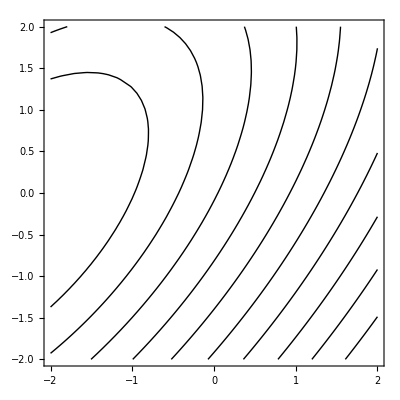

```mathematica
ContourPlot[Sqrt@loss2[v2c@{x,y}],{x,-2,2},{y,-2,2},Contours->10,ContourShading->None]
```

```mathematica
toscalar@loss2[wopt-w0]==loss[wopt]
```

True

```mathematica
grad[w0]==w0ᵀ.A
```

False

## Directional curve

```mathematica
d=v2c@{1,0};
loss3[eps_]:=loss[w0]+1/2 eps^2 dᵀ.A.d+eps dᵀ.grad[w0]
```

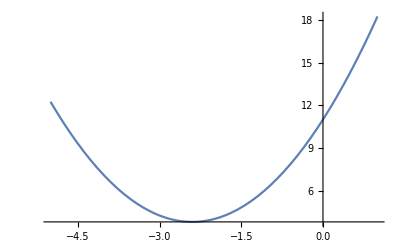

```mathematica
Plot[loss3[eps],{eps,-3-2,3-2}]
```

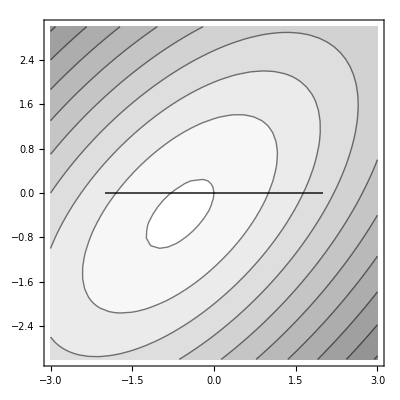

```mathematica
plt1=ContourPlot[Sqrt@loss[v2c@{x1,x2}],{x1,-3,3},{x2,-3,3},ColorFunction->Function[GrayLevel[1 - .45 #]]];
Show[plt1,Graphics[Line[{{-2,0},{2,0}}]]]
```

```mathematica
(dᵀ.grad[w0])/(dᵀ.A.d)
```

{{12/5}}

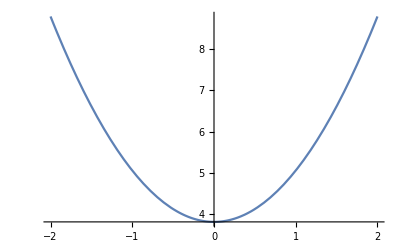

```mathematica
Plot[loss3[eps-12/5],{eps,-2,2}]
```